# Prerešetani sinus

## Slika

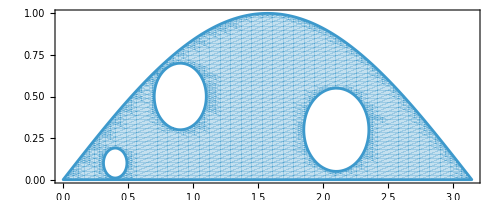

```mathematica
RegionPlot[
y<=Sin[x]
&&(x-0.9)^2+(y-0.5)^2>0.2^2
&&(x-0.4)^2+(y-0.1)^2>0.09^2
&&(x-2.1)^2+(y-0.3)^2>0.25^2
,{x,0,π},{y,0,1},
PlotPoints->40,
AspectRatio->Automatic]
```

## Izračun površine z Mathematico

ImplicitRegion[y≤Sin[x]&&(-0.9+x)^2+(-0.5+y)^2>0.04&&(-0.4+x)^2+(-0.1+y)^2>0.0081&&(-2.1+x)^2+(-0.7+y)^2>0.0625&&0≤x≤π&&0≤y≤1,{x,y}]

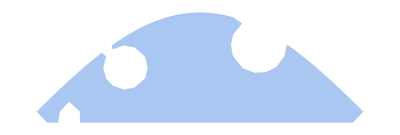

```mathematica
Region[preresetaniSinus]
```

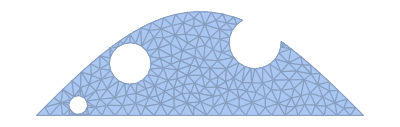

```mathematica
DiscretizeRegion[Region[preresetaniSinus]]
```

```mathematica
Area[Region[preresetaniSinus]]
```

1.6846

## Izračun površine z metodo Monte-Carlo

```mathematica
steviloTock=1000;
tocke=Table[{RandomReal[{0,π}],RandomReal[{0,1}]},{steviloTock}];
vRegiji=Select[tocke,pogoj];
```

```mathematica
N[Length[vRegiji]/steviloTock*π]
```

1.71845

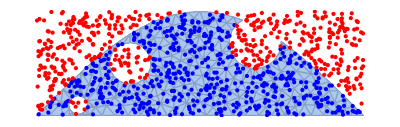

```mathematica
Show[
DiscretizeRegion[Region[preresetaniSinus]],
Graphics[{
Blue,
Point[vRegiji],
Red,
Point[Complement[tocke,vRegiji]]
}]
]
```

## Manipulate

```mathematica
Table[Sin[k x],{k,1,10}]
```

{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x],Sin[6 x],Sin[7 x],Sin[8 x],Sin[9 x],Sin[10 x]}

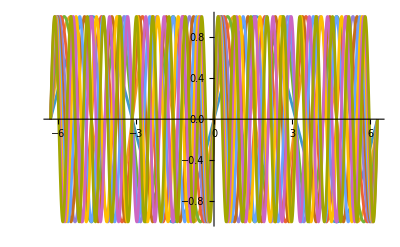

```mathematica
grafi=Table[Sin[k x],{k,1,10}];
Plot[grafi,{x,-2π,2π}]
```

```mathematica
?Plot
```

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x],Sin[6 x],Sin[7 x],Sin[8 x],Sin[9 x],Sin[10 x]},{x,-2π,2π},Options->]
```

-Graphics-

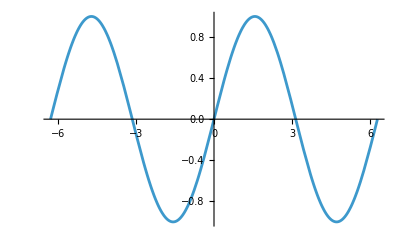
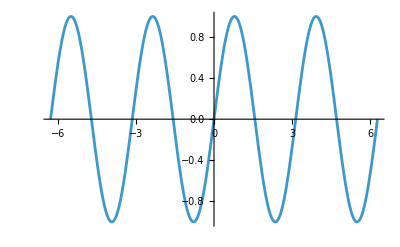
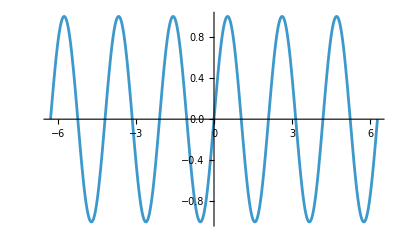
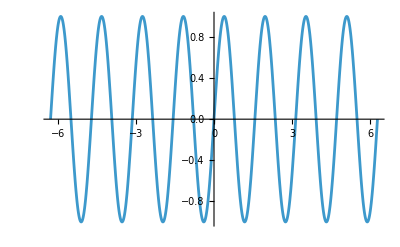
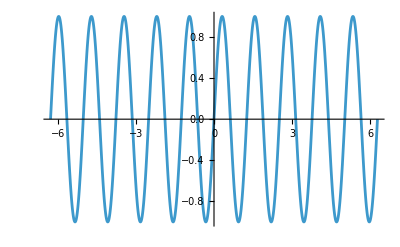
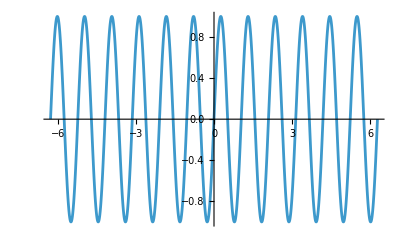
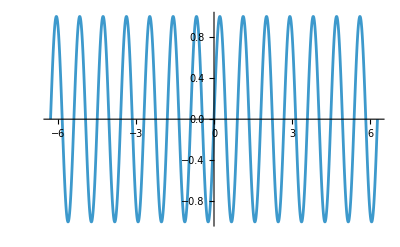
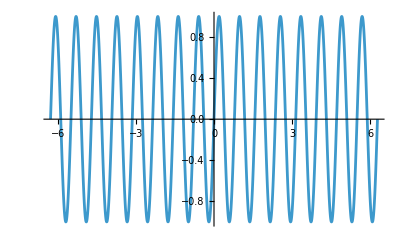

```mathematica
Table[Plot[Sin[k x],{x,-2π,2π}],{k,1,10}]
```

```mathematica
Manipulate[Plot[Sin[k x],{x,-2π,2π}],{k,{1,2,5,10}}]
```

```mathematica
?Manipulate
```

```mathematica
?DistanceFunction
```

```mathematica
&&(x-0.9)^2+(y-0.5)^2>0.2^2
&&(x-0.4)^2+(y-0.1)^2>0.09^2
&&(x-2.1)^2+(y-0.3)^2>0.25^2
```

```mathematica
vseTocke=Table[{RandomReal[{0,π}],RandomReal[{0,1}]},{10000}];
Manipulate[
pogoj[{x_,y_}]:=y<=Sin[x]&&(x-t0[[1]])^2+(y-t0[[2]])^2>Norm[r0-t0]^2&&
y<=Sin[x]&&(x-t1[[1]])^2+(y-t1[[2]])^2>Norm[r1-t1]^2&&
y<=Sin[x]&&(x-t2[[1]])^2+(y-t2[[2]])^2>Norm[r2-t2]^2;
preresetaniSinus=ImplicitRegion[pogoj[{x,y}],{{x,0,π},{y,0,1}}];tocke=Take[vseTocke,steviloTock];
vRegiji=Select[tocke,pogoj];
Column[{
Show[
Graphics[{
Blue,
Point[vRegiji],
Red,
Point[Complement[tocke,vRegiji]]
}]
],
N[Length[vRegiji]/steviloTock*π]
}],{{steviloTock,1000},100,10000,100},{{t0,{0.9,0.5}},{0,0},{π,1},Locator},
{{r0,{0.9+0.2,0.5}},{0,0},{π,1},Locator},
{{t1,{0.4,0.1}},{0,0},{π,1},Locator},
{{r1,{0.4+0.09,0.1}},{0,0},{π,1},Locator},
{{t2,{2.1,0.3}},{0,0},{π,1},Locator},
{{r2,{2.1+0.25,0.3}},{0,0},{π,1},Locator}
]
```

```mathematica
?Locator
```